```mathematica
LaneEmden=1/ξ^2 D[(ξ^2 D[θ[ξ], ξ]), ξ]+θ[ξ]^n==0;

sols=NDSolve[{LaneEmden/.n->5/3,θ[0.01]==1,θ'[0.01]==0},θ,{ξ,0.01,10}, MaxSteps->100000, Method->"ExplicitRungeKutta"]
```

{{θ→InterpolatingFunction[{{0.01,10.}},<>]}}

InterpolatingFunction::dmval: Input value {0.000204286} lies outside the range of data in the interpolating function. Extrapolation will be used.

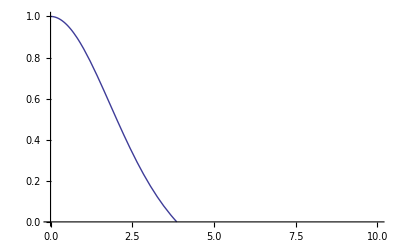

```mathematica
Plot[θ[ξ]/.sols,{ξ,0,10}]
```

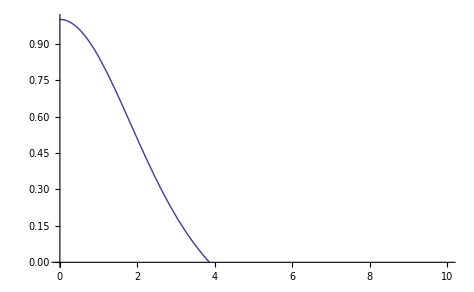

```mathematica
vals=θ/.First[sols]
```

InterpolatingFunction[{{0.01,10.}},<>]

```mathematica
vals[4]
```

-0.0233035+3.25394×10^-6 ⅈ

```mathematica
data=Table[{i,vals[i]},{i,0.01,10,0.01}];
```

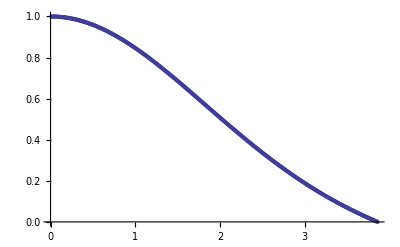

```mathematica
ListPlot[data]
```

```mathematica
str=OpenWrite["/Users/kaitlin/TALENT/project1/laneEmbden.txt"]
```

OutputStream[/Users/kaitlin/TALENT/project1/laneEmbden.txt,282]

```mathematica
Write[str,data]
```

```mathematica
Close[str]
```

/Users/kaitlin/TALENT/project1/laneEmbden.txt

```mathematica
FilePrint[%];
```

{{0.01, 1.}, {0.02, 0.9999666670677589}, {0.03, 0.9998888940563162}, 
 {0.04, 0.9997750224712131}, {0.05, 0.999626730645049}, 
 {0.060000000000000005, 0.9994445890892569}, 
 {0.06999999999999999, 0.9992288542017086}, {0.08, 0.9989796666725196}, 
 {0.09, 0.9986971176144458}, {0.09999999999999999, 0.998381274948406}, 
 {0.11, 0.9980321955224305}, {0.12, 0.9976499310438898}, 
 {0.13, 0.9972345313208707}, {0.14, 0.9967860461557003}, 
 {0.15000000000000002, 0.9963045263789057}, {0.16, 0.995790024561803}, 
 {0.17, 0.9952425954747026}, {0.18000000000000002, 0.9946622963617137}, 
 {0.19, 0.9940491871155711}, {0.2, 0.993403330429299}, 
 {0.21000000000000002, 0.9927247918901418}, {0.22, 0.992013640038197}, 
 {0.23, 0.9912699464028214}, {0.24000000000000002, 0.9904937855257593}, 
 {0.25, 0.9896852349841347}, {0.26, 0.9888443754045882}, 
 {0.27, 0.9879712904608341}, {0.28, 0.9870660668753347}, 
 {0.29000000000000004, 0.9861287944108388}, {0.3, 0.9851595658605118}, 
 {0.31, 0.9841584770380669}, {0.32, 0.9831256267678959}, 
 {0.33, 0.9820611168726565}, {0.34, 0.9809650521536788}, 
 {0.35000000000000003, 0.9798375403776324}, {0.36000000000000004, 
  0.9786786922575428}, {0.37, 0.9774886214320496}, 
 {0.38, 0.9762674444446635}, {0.39, 0.9750152807230228}, 
 {0.4, 0.9737322525581509}, {0.41000000000000003, 0.9724184850837139}, 
 {0.42000000000000004, 0.9710741062542452}, {0.43, 0.9696992468171872}, 
 {0.44, 0.9682940402923574}, {0.45, 0.9668586229483013}, 
 {0.46, 0.9653931337750993}, {0.47000000000000003, 0.9638977144571588}, 
 {0.48000000000000004, 0.9623725093460049}, {0.49, 0.9608176654330723}, 
 {0.5, 0.9592333323224964}, {0.51, 0.9576196622039052}, 
 {0.52, 0.9559768098252099}, {0.53, 0.9543049324653972}, 
 {0.54, 0.9526041899043137}, {0.55, 0.9508747443870373}, 
 {0.56, 0.9491167606013222}, {0.5700000000000001, 0.9473304056474393}, 
 {0.5800000000000001, 0.9455158490055304}, {0.59, 0.943673262502962}, 
 {0.6, 0.9418028202816794}, {0.61, 0.9399046987655608}, 
 {0.62, 0.9379790766277717}, {0.63, 0.9360261347581182}, 
 {0.64, 0.9340460562304019}, {0.65, 0.9320390262697734}, 
 {0.66, 0.9300052322200867}, {0.67, 0.9279448635112529}, 
 {0.68, 0.9258581116265947}, {0.6900000000000001, 0.923745170066621}, 
 {0.7000000000000001, 0.9216062343058707}, {0.7100000000000001, 
  0.9194415017668027}, {0.72, 0.9172511717859675}, 
 {0.73, 0.9150354455772113}, {0.74, 0.9127945261948816}, 
 {0.75, 0.9105286184970307}, {0.76, 0.9082379291086212}, 
 {0.77, 0.9059226663847301}, {0.78, 0.9035830403737529}, 
 {0.79, 0.9012192627806094}, {0.8, 0.898831546929947}, 
 {0.81, 0.8964201077293465}, {0.8200000000000001, 0.8939851616325256}, 
 {0.8300000000000001, 0.8915269266025438}, {0.8400000000000001, 
  0.8890456220750077}, {0.85, 0.8865414689212743}, 
 {0.86, 0.8840146894116568}, {0.87, 0.8814655071786285}, 
 {0.88, 0.8788941471799105}, {0.89, 0.8763008356585636}, 
 {0.9, 0.873685800101735}, {0.91, 0.8710492692030458}, 
 {0.92, 0.868391472824874}, {0.93, 0.8657126419606046}, 
 {0.9400000000000001, 0.8630130086968805}, {0.9500000000000001, 
  0.8602928061758524}, {0.9600000000000001, 0.8575522685574298}, 
 {0.97, 0.8547916309815313}, {0.98, 0.852011129530335}, 
 {0.99, 0.8492110011905288}, {1., 0.8463914838155615}, 
 {1.01, 0.8435528160878927}, {1.02, 0.8406952374812433}, 
 {1.03, 0.8378189882228463}, {1.04, 0.834924309255697}, 
 {1.05, 0.8320114422008039}, {1.06, 0.8290806293194383}, 
 {1.07, 0.8261321134753857}, {1.08, 0.823166138097196}, 
 {1.09, 0.8201829471404335}, {1.1, 0.8171827850499281}, 
 {1.11, 0.8141658967220253}, {1.12, 0.8111325274668367}, 
 {1.1300000000000001, 0.8080829229740831}, {1.1400000000000001, 
  0.80501732930167}, {1.1500000000000001, 0.8019359928171452}, 
 {1.1600000000000001, 0.7988391601450178}, {1.17, 0.7957270781332786}, 
 {1.18, 0.7925999938200888}, {1.19, 0.7894581544004685}, 
 {1.2, 0.7863018071929849}, {1.21, 0.783131199606441}, 
 {1.22, 0.7799465791065637}, {1.23, 0.776748193182693}, 
 {1.24, 0.7735362893144693}, {1.25, 0.7703111149385229}, 
 {1.26, 0.767072917415162}, {1.27, 0.7638219439950614}, 
 {1.28, 0.7605584417859504}, {1.29, 0.757282657719302}, 
 {1.3, 0.7539948385170208}, {1.31, 0.7506952306581315}, 
 {1.32, 0.7473840803454678}, {1.33, 0.7440616334723605}, 
 {1.34, 0.7407281355893259}, {1.35, 0.7373838318707546}, 
 {1.36, 0.7340289670815994}, {1.37, 0.7306637855440643}, 
 {1.3800000000000001, 0.7272885311042927}, {1.3900000000000001, 
  0.7239034470990559}, {1.4000000000000001, 0.7205087763224416}, 
 {1.4100000000000001, 0.7171047609977306}, {1.42, 0.713691642819483}, 
 {1.43, 0.7102696628989714}, {1.44, 0.7068390616722133}, 
 {1.45, 0.7034000788747728}, {1.46, 0.6999529535184833}, 
 {1.47, 0.6964979238681706}, {1.48, 0.6930352274183752}, 
 {1.49, 0.6895651008700758}, {1.5, 0.6860877801074116}, 
 {1.51, 0.6826035001744049}, {1.52, 0.6791124952516843}, 
 {1.53, 0.6756149986332073}, {1.54, 0.6721112427029832}, 
 {1.55, 0.6686014589117957}, {1.56, 0.6650858777539259}, 
 {1.57, 0.661564728743875}, {1.58, 0.6580382403930867}, 
 {1.59, 0.6545066401866707}, {1.6, 0.6509701545601251}, 
 {1.61, 0.647429008876059}, {1.62, 0.6438834274009158}, 
 {1.6300000000000001, 0.6403336332816952}, {1.6400000000000001, 
  0.6367798485226771}, {1.6500000000000001, 0.6332222939621431}, 
 {1.6600000000000001, 0.6296611892491004}, {1.6700000000000002, 
  0.626096752820004}, {1.68, 0.6225292018754794}, {1.69, 0.6189587523570458}, 
 {1.7, 0.6153856189238387}, {1.71, 0.6118100149293323}, 
 {1.72, 0.6082321523980632}, {1.73, 0.6046522420023522}, 
 {1.74, 0.6010704930802746}, {1.75, 0.5974871137383229}, 
 {1.76, 0.5939023107097102}, {1.77, 0.5903162893013862}, 
 {1.78, 0.5867292533838935}, {1.79, 0.5831414053812238}, 
 {1.8, 0.5795529462606752}, {1.81, 0.5759640755227078}, 
 {1.82, 0.5723749911908005}, {1.83, 0.5687858898013075}, 
 {1.84, 0.5651969663933146}, {1.85, 0.5616084144984961}, 
 {1.86, 0.5580204261309706}, {1.87, 0.554433191777158}, 
 {1.8800000000000001, 0.5508469003856356}, {1.8900000000000001, 
  0.5472617393569948}, {1.9000000000000001, 0.5436778945336976}, 
 {1.9100000000000001, 0.5400955501899329}, {1.9200000000000002, 
  0.5365148890214729}, {1.93, 0.5329360921355297}, 
 {1.94, 0.5293593390406119}, {1.95, 0.5257848076363807}, 
 {1.96, 0.5222126742035066}, {1.97, 0.518643113393526}, 
 {1.98, 0.5150762982186972}, {1.99, 0.5115124000418575}, 
 {2., 0.507951588566279}, {2.01, 0.5043940318255256}, 
 {2.02, 0.5008398961733088}, {2.03, 0.4972893462733455}, 
 {2.04, 0.4937425450892125}, {2.05, 0.49019965387420483}, 
 {2.0599999999999996, 0.486660832161191}, {2.07, 0.48312623775246977}, 
 {2.0799999999999996, 0.47959602670962725}, {2.09, 0.47607035334648806}, 
 {2.0999999999999996, 0.4725493703364937}, {2.11, 0.46903322874382214}, 
 {2.1199999999999997, 0.4655220778790764}, {2.13, 0.4620160652908848}, 
 {2.1399999999999997, 0.4585153367679046}, {2.15, 0.4550200363408229}, 
 {2.1599999999999997, 0.45153030628435986}, {2.17, 0.44804628711926986}, 
 {2.1799999999999997, 0.44456811761434445}, {2.19, 0.4410959347884138}, 
 {2.1999999999999997, 0.43762987391234975}, {2.21, 0.4341700685110667}, 
 {2.2199999999999998, 0.43071665036552514}, {2.23, 0.42726974951473246}, 
 {2.2399999999999998, 0.4238294942577464}, {2.25, 0.4203960111556758}, 
 {2.26, 0.4169694250336843}, {2.27, 0.4135498589829908}, 
 {2.28, 0.41013743436287325}, {2.29, 0.4067322708026694}, 
 {2.3, 0.40333448620377993}, {2.31, 0.3999441967416699}, 
 {2.32, 0.3965615168678718}, {2.3299999999999996, 0.39318655931198626}, 
 {2.34, 0.38981943508368555}, {2.3499999999999996, 0.38646025347471535}, 
 {2.36, 0.3831091220608962}, {2.3699999999999997, 0.37976614670412684}, 
 {2.38, 0.3764314315543851}, {2.3899999999999997, 0.3731050790517311}, 
 {2.4, 0.3697871899283087}, {2.4099999999999997, 0.36647786321034814}, 
 {2.42, 0.36317719622016753}, {2.4299999999999997, 0.35988528457817587}, 
 {2.44, 0.3566022222048742}, {2.4499999999999997, 0.3533281013228588}, 
 {2.46, 0.3500630124588223}, {2.4699999999999998, 0.3468070444455569}, 
 {2.48, 0.34356028442395514}, {2.4899999999999998, 0.3403228178450137}, 
 {2.5, 0.3370947284737217}, {2.51, 0.33387609848082567}, 
 {2.52, 0.33066700849407304}, {2.53, 0.32746753749433033}, 
 {2.54, 0.32427776281546017}, {2.55, 0.3210977601536687}, 
 {2.56, 0.31792760357685024}, {2.57, 0.31476736553393453}, 
 {2.5799999999999996, 0.31161711686423166}, {2.59, 0.3084769268067785}, 
 {2.5999999999999996, 0.305346863009685}, {2.61, 0.3022269915394793}, 
 {2.6199999999999997, 0.2991173768904547}, {2.63, 0.29601808199401464}, 
 {2.6399999999999997, 0.29292916822801973}, {2.65, 0.28985069542613257}, 
 {2.6599999999999997, 0.28678272188716497}, {2.67, 0.28372530438442267}, 
 {2.6799999999999997, 0.28067849817505236}, {2.69, 0.27764235700938694}, 
 {2.6999999999999997, 0.27461693314029206}, {2.71, 0.27160227733251135}, 
 {2.7199999999999998, 0.26859843887201346}, {2.73, 0.26560546557533676}, 
 {2.7399999999999998, 0.26262340379893656}, {2.75, 0.25965229844853}, 
 {2.76, 0.2566921929884431}, {2.77, 0.2537431294509554}, 
 {2.78, 0.2508051484456475}, {2.79, 0.24787828916874546}, 
 {2.8, 0.2449625894124683}, {2.81, 0.24205808557437242}, 
 {2.82, 0.23916481266669914}, {2.8299999999999996, 0.23628280432571935}, 
 {2.84, 0.2334120928210801}, {2.8499999999999996, 0.23055270906515085}, 
 {2.86, 0.22770468262236865}, {2.8699999999999997, 0.224868041718585}, 
 {2.88, 0.2220428132504109}, {2.8899999999999997, 0.21922902279456385}, 
 {2.9, 0.2164266946172128}, {2.9099999999999997, 0.21363585168332505}, 
 {2.92, 0.21085651566601132}, {2.9299999999999997, 0.20808870695587267}, 
 {2.94, 0.2053324446703455}, {2.9499999999999997, 0.20258774666304852}, 
 {2.96, 0.1998546295331277}, {2.9699999999999998, 0.1971331086346033}, 
 {2.98, 0.19442319808571473}, {2.9899999999999998, 0.19172491077788212}, 
 {3., 0.1890382583912149}, {3.01, 0.1863632514234327}, 
 {3.02, 0.18369989920356675}, {3.03, 0.18104820990118914}, 
 {3.04, 0.17840819053563584}, {3.05, 0.1757798469852314}, 
 {3.06, 0.17316318399651193}, {3.07, 0.17055820519344986}, 
 {3.08, 0.16796491308667688}, {3.09, 0.1653833090827088}, 
 {3.0999999999999996, 0.16281339349316842}, {3.11, 0.16025516554401004}, 
 {3.1199999999999997, 0.15770862338474334}, {3.13, 0.1551737640976566}, 
 {3.1399999999999997, 0.15265058370704157}, {3.15, 0.15013907718841624}, 
 {3.1599999999999997, 0.14763923847774968}, {3.17, 0.14515106048068505}, 
 {3.1799999999999997, 0.1426745350817643}, {3.19, 0.14020965315365116}, 
 {3.1999999999999997, 0.1377564045663559}, {3.21, 0.1353147781964583}, 
 {3.2199999999999998, 0.13288476193633236}, {3.23, 0.13046634270336932}, 
 {3.2399999999999998, 0.12805950644920244}, {3.25, 0.12566423816892994}, 
 {3.26, 0.12328052191033967}, {3.27, 0.12090834078313227}, 
 {3.28, 0.11854767696814572}, {3.29, 0.11619851172657847}, 
 {3.3, 0.11386082540921408}, {3.31, 0.1115345974656443}, 
 {3.32, 0.1092198064534937}, {3.33, 0.10691643004764279}, 
 {3.34, 0.10462444504945258}, {3.3499999999999996, 0.10234382739598788}, 
 {3.36, 0.10007455216924135}, {3.3699999999999997, 0.09781659360535772}, 
 {3.38, 0.09556992510385692}, {3.3899999999999997, 0.0933345192368588}, 
 {3.4, 0.09111034775830609}, {3.4099999999999997, 0.08889738161318918}, 
 {3.42, 0.0866955909467691}, {3.4299999999999997, 0.08450494511380222}, 
 {3.44, 0.0823254126877633}, {3.4499999999999997, 0.08015696147007016}, 
 {3.46, 0.07799955849930675}, {3.4699999999999998, 0.07585317006044776}, 
 {3.48, 0.07371776169407541 + 0.*I}, {3.4899999999999998, 
  0.07159329817725502 + 0.*I}, {3.5, 0.06947974346244676 + 0.*I}, 
 {3.51, 0.06737706074920771 + 0.*I}, {3.52, 0.06528521250455069 + 0.*I}, 
 {3.53, 0.06320416046479771 + 0.*I}, {3.54, 0.061133865637432006 + 0.*I}, 
 {3.55, 0.05907428830295153 + 0.*I}, {3.56, 0.057025388016720885 + 0.*I}, 
 {3.57, 0.054987123610824876 + 0.*I}, {3.58, 0.05295945319592047 + 0.*I}, 
 {3.59, 0.0509423341630903 + 0.*I}, {3.5999999999999996, 
  0.04893572318569472 + 0.*I}, {3.61, 0.04693957622122488 + 0.*I}, 
 {3.6199999999999997, 0.0449538485131557 + 0.*I}, 
 {3.63, 0.04297849459279799 + 0.*I}, {3.6399999999999997, 
  0.041013468281151884 + 0.*I}, {3.65, 0.0390587226907589 + 0.*I}, 
 {3.6599999999999997, 0.03711421022755537 + 0.*I}, 
 {3.67, 0.03517988259272451 + 0.*I}, {3.6799999999999997, 
  0.03325569078454979 + 0.*I}, {3.69, 0.03134158509897292 + 0.*I}, 
 {3.6999999999999997, 0.02943751509342543 + 0.*I}, 
 {3.71, 0.0275434295815648 + 0.*I}, {3.7199999999999998, 
  0.025659276662987816 + 0.*I}, {3.73, 0.023785003703978954 + 0.*I}, 
 {3.7399999999999998, 0.02192055731539757 + 0.*I}, 
 {3.75, 0.02006588333056383 + 0.*I}, {3.76, 0.018220926783145894 + 0.*I}, 
 {3.77, 0.016385631885045857 + 0.*I}, {3.78, 0.014559942004286938 + 0.*I}, 
 {3.79, 0.012743799642899399 + 0.*I}, {3.8, 0.010937146414807749 + 0.*I}, 
 {3.81, 0.009139923020198962 + 0.*I}, {3.82, 0.007352069143398248 + 0.*I}, 
 {3.83, 0.005573523428568516 + 0.*I}, {3.84, 0.003804223387933477 + 0.*I}, 
 {3.8499999999999996, 0.0020441051380623177 + 0.*I}, 
 {3.86, 0.0002931031289231424 + 1.6172824107795576*^-15*I}, 
 {3.8699999999999997, -0.0014488503914918509 + 1.6356065750334913*^-10*I}, 
 {3.88, -0.0031818258426331465 + 2.18844883200562*^-9*I}, 
 {3.8899999999999997, -0.004905894809181505 + 1.0209319715373456*^-8*I}, 
 {3.9, -0.006621129468384713 + 3.048099080787219*^-8*I}, 
 {3.9099999999999997, -0.008327602302177045 + 7.097374094551662*^-8*I}, 
 {3.92, -0.010025385821935105 + 1.4098282748888991*^-7*I}, 
 {3.9299999999999997, -0.011714552532460006 + 2.510116276729743*^-7*I}, 
 {3.94, -0.013395174983211454 + 4.127778333296388*^-7*I}, 
 {3.9499999999999997, -0.015067325683156642 + 6.390829736826068*^-7*I}, 
 {3.96, -0.016731077066002693 + 9.437394466550439*^-7*I}, 
 {3.9699999999999998, -0.018386501457889125 + 1.3415006573542477*^-6*I}, 
 {3.98, -0.020033671054697576 + 1.8480088852516923*^-6*I}, 
 {3.9899999999999998, -0.021672657897078777 + 2.4797376834991054*^-6*I}, 
 {4., -0.023303533847690974 + 3.2539387172543234*^-6*I}, 
 {4.01, -0.02492637057936534 + 4.188609503346033*^-6*I}, 
 {4.02, -0.026541239563672173 + 5.302461908261485*^-6*I}, 
 {4.03, -0.028148212059486453 + 6.614890646134011*^-6*I}, 
 {4.04, -0.029747359101553003 + 8.145941776730068*^-6*I}, 
 {4.05, -0.03133875148905307 + 9.916281203437439*^-6*I}, 
 {4.06, -0.032922459774169396 + 0.000011947163171252288*I}, 
 {4.07, -0.03449855425065223 + 0.000014260398764767008*I}, 
 {4.08, -0.036067104943715574 + 0.000016878327179256246*I}, 
 {4.09, -0.03762818161093481 + 0.000019823809329105723*I}, 
 {4.1, -0.0391818537339961 + 0.00002312020149205138*I}, 
 {4.109999999999999, -0.04072819050990675 + 0.000026791329160318158*I}, 
 {4.12, -0.04226726084705964 + 0.00003086147143391393*I}, 
 {4.13, -0.043799133361338324 + 0.00003535534550201769*I}, 
 {4.14, -0.04532387637222365 + 0.00004029809112437144*I}, 
 {4.1499999999999995, -0.046841557898898864 + 0.000045715255112668375*I}, 
 {4.16, -0.04835224565635565 + 0.00005163277581194348*I}, 
 {4.17, -0.04985600705149931 + 0.000058076967581961104*I}, 
 {4.18, -0.05135290917925525 + 0.00006507450527860775*I}, 
 {4.1899999999999995, -0.05284301881867422 + 0.00007265240873527967*I}, 
 {4.2, -0.05432640242912102 + 0.00008083802749538023*I}, 
 {4.21, -0.05580312615057237 + 0.00008965903758963569*I}, 
 {4.22, -0.05727325580299475 + 0.00009914343353400963*I}, 
 {4.2299999999999995, -0.05873685687967266 + 0.00010931950276238037*I}, 
 {4.24, -0.06019399454566661 + 0.00012021581675439742*I}, 
 {4.25, -0.06164473363673004 + 0.00013186122359993934*I}, 
 {4.26, -0.0630891386582275 + 0.00014428484056358117*I}, 
 {4.27, -0.06452727378405156 + 0.0001575160466490529*I}, 
 {4.28, -0.06595920285554045 + 0.00017158447516370348*I}, 
 {4.29, -0.067384989380395 + 0.0001865200062829575*I}, 
 {4.3, -0.06880469653159679 + 0.00020235275961478483*I}, 
 {4.31, -0.07021838714632506 + 0.00021911308676415746*I}, 
 {4.32, -0.07162612372487437 + 0.0002368315638975143*I}, 
 {4.33, -0.0730279684295715 + 0.00025553898430721666*I}, 
 {4.34, -0.07442398308369366 + 0.0002752663509760196*I}, 
 {4.35, -0.07581422917038534 + 0.0002960448691415276*I}, 
 {4.36, -0.07719876783157602 + 0.00031790593886066017*I}, 
 {4.37, -0.07857765986689706 + 0.0003408811475741057*I}, 
 {4.38, -0.07995096573259985 + 0.0003650022626707949*I}, 
 {4.39, -0.08131874554058008 + 0.00039030122464637574*I}, 
 {4.3999999999999995, -0.08268105906042966 + 0.00041681015593129163*I}, 
 {4.41, -0.08403796572016065 + 0.00044456135848762565*I}, 
 {4.42, -0.08538952460336524 + 0.0004735872942800641*I}, 
 {4.43, -0.0867357944488853 + 0.0005039205818025423*I}, 
 {4.4399999999999995, -0.0880768336506372 + 0.000535593993523732*I}, 
 {4.45, -0.08941270025743743 + 0.0005686404533325428*I}, 
 {4.46, -0.09074345197282724 + 0.000603093033983606*I}, 
 {4.47, -0.09206914615489875 + 0.0006389849545427894*I}, 
 {4.4799999999999995, -0.09338983981611972 + 0.0006763495778326816*I}, 
 {4.49, -0.09470558962315906 + 0.0007152204078780944*I}, 
 {4.5, -0.09601645189671165 + 0.0007556310873515458*I}, 
 {4.51, -0.09732248261132433 + 0.0007976153950187766*I}, 
 {4.52, -0.0986237373952207 + 0.0008412072431842327*I}, 
 {4.53, -0.09992027153012668 + 0.0008864406751365699*I}, 
 {4.54, -0.10121213995109521 + 0.0009333498625941326*I}, 
 {4.55, -0.10249939724633236 + 0.0009819691031504756*I}, 
 {4.56, -0.10378209765702208 + 0.0010323328177198432*I}, 
 {4.57, -0.1050602950771517 + 0.0010844755479826754*I}, 
 {4.58, -0.1063340430533368 + 0.001138431953831084*I}, 
 {4.59, -0.10760339478464714 + 0.0011942368108143787*I}, 
 {4.6, -0.1088684031224315 + 0.0012519250075845427*I}, 
 {4.61, -0.11012912057014317 + 0.0013115315433417409*I}, 
 {4.62, -0.11138559928316479 + 0.001373091525279794*I}, 
 {4.63, -0.11263789106814664 + 0.0014366401715078295*I}, 
 {4.64, -0.11388604738193184 + 0.0015022128261955973*I}, 
 {4.6499999999999995, -0.11513011933386805 + 0.0015698449429372473*I}, 
 {4.66, -0.11637015768612832 + 0.0016395720793192974*I}, 
 {4.67, -0.1176062128533536 + 0.0017114298971712808*I}, 
 {4.68, -0.11883833490229635 + 0.0017854541628164584*I}, 
 {4.6899999999999995, -0.12006657355146304 + 0.0018616807473224666*I}, 
 {4.7, -0.12129097817075735 + 0.0019401456267520057*I}, 
 {4.71, -0.12251159778112267 + 0.002020884882413487*I}, 
 {4.72, -0.12372848105418571 + 0.0021039347011117477*I}, 
 {4.7299999999999995, -0.12494167631189902 + 0.002189331375398698*I}, 
 {4.74, -0.12615123152618413 + 0.0022771113038240103*I}, 
 {4.75, -0.12735719431857406 + 0.002367310991185763*I}, 
 {4.76, -0.12855961195985707 + 0.0024599670487811588*I}, 
 {4.77, -0.12975853136971896 + 0.0025551161946571724*I}, 
 {4.78, -0.13095399911638633 + 0.002652795253861237*I}, 
 {4.79, -0.1321460614162692 + 0.0027530411586918864*I}, 
 {4.8, -0.13333476413360443 + 0.0028558909489494804*I}, 
 {4.81, -0.13452015278009838 + 0.0029613817721868448*I}, 
 {4.82, -0.13570227251457 + 0.0030695508839599646*I}, 
 {4.83, -0.13688116814259343 + 0.0031804356480786182*I}, 
 {4.84, -0.1380568841161415 + 0.0032940735368571115*I}, 
 {4.85, -0.1392294645332283 + 0.003410502131364912*I}, 
 {4.86, -0.14039895313755232 + 0.003529759121677345*I}, 
 {4.87, -0.14156539331813908 + 0.003651882307126223*I}, 
 {4.88, -0.1427288281089846 + 0.0037769095965505864*I}, 
 {4.89, -0.14388930018869794 + 0.0039048790085473347*I}, 
 {4.8999999999999995, -0.14504685188014432 + 0.004035828671721911*I}, 
 {4.91, -0.1462015251500881 + 0.004169796824938986*I}, 
 {4.92, -0.14735336160883547 + 0.0043068218175730906*I}, 
 {4.93, -0.14850240250987773 + 0.004446942109759426*I}, 
 {4.9399999999999995, -0.14964868874566065 + 0.004590196277313746*I}, 
 {4.95, -0.1507922608376345 + 0.0047366230256925945*I}, 
 {4.96, -0.15193315894792223 + 0.004886261179380113*I}, 
 {4.97, -0.15307142288150877 + 0.005039149679673709*I}, 
 {4.9799999999999995, -0.15420709208486374 + 0.005195327586296427*I}, 
 {4.99, -0.1553402056445647 + 0.005354834079009386*I}, 
 {5., -0.15647080228591975 + 0.005517708459224149*I}, 
 {5.01, -0.15759892037159148 + 0.005683990151615221*I}, 
 {5.02, -0.15872459790021937 + 0.005853718705732417*I}, 
 {5.03, -0.15984787250504318 + 0.006026933797613304*I}, 
 {5.04, -0.1609687814525257 + 0.006203675231395566*I}, 
 {5.05, -0.16208736164097626 + 0.006383982940929506*I}, 
 {5.06, -0.16320364959917366 + 0.00656789699139041*I}, 
 {5.07, -0.16431768148498926 + 0.0067554575808909945*I}, 
 {5.08, -0.16542949308400967 + 0.006946705042093761*I}, 
 {5.09, -0.16653911980816055 + 0.007141679843823511*I}, 
 {5.1, -0.1676465966943292 + 0.007340422592679703*I}, 
 {5.11, -0.16875195840298782 + 0.007542974034648903*I}, 
 {5.12, -0.16985523921681636 + 0.00774937505671713*I}, 
 {5.13, -0.170956473039326 + 0.007959666688482386*I}, 
 {5.14, -0.17205569339348192 + 0.008173890103767*I}, 
 {5.1499999999999995, -0.17315293342032653 + 0.008392086622230066*I}, 
 {5.16, -0.17424822587760255 + 0.008614297710979884*I}, 
 {5.17, -0.1753416031383758 + 0.008840564986186294*I}, 
 {5.18, -0.17643309718965877 + 0.009070930214693216*I}, 
 {5.1899999999999995, -0.17752273963103346 + 0.009305435315630996*I}, 
 {5.2, -0.17861056167327446 + 0.00954412236202885*I}, 
 {5.21, -0.17969659413697184 + 0.009787033582427218*I}, 
 {5.22, -0.18078086745115463 + 0.010034211362490294*I}, 
 {5.2299999999999995, -0.18186341165191375 + 0.010285698246618366*I}, 
 {5.24, -0.182944256381025 + 0.010541536939560281*I}, 
 {5.25, -0.184023430884572 + 0.010801770308025769*I}, 
 {5.26, -0.1851009640115697 + 0.011066441382297999*I}, 
 {5.27, -0.1861768842125872 + 0.011335593357845905*I}, 
 {5.28, -0.18725121953837093 + 0.011609269596936662*I}, 
 {5.29, -0.18832399763846736 + 0.01188751363024799*I}, 
 {5.3, -0.1893952457598467 + 0.012170369158480732*I}, 
 {5.31, -0.19046499074552556 + 0.012457880053971176*I}, 
 {5.32, -0.19153325902726293 + 0.01275009036213181*I}, 
 {5.33, -0.1926000765932949 + 0.01304704430332189*I}, 
 {5.34, -0.1936654690116136 + 0.013348786277889484*I}, 
 {5.35, -0.19472946144211564 + 0.013655360868807753*I}, 
 {5.36, -0.19579207863325765 + 0.013966812843309268*I}, 
 {5.37, -0.19685334491867515 + 0.014283187154518415*I}, 
 {5.38, -0.19791328421380203 + 0.014604528943084078*I}, 
 {5.39, -0.19897192001248928 + 0.014930883538812074*I}, 
 {5.3999999999999995, -0.20002927538362428 + 0.015262296462297695*I}, 
 {5.41, -0.20108537296774973 + 0.01559881342655827*I}, 
 {5.42, -0.20214023497368255 + 0.015940480338665568*I}, 
 {5.43, -0.2031938831751334 + 0.0162873433013785*I}, 
 {5.4399999999999995, -0.2042463389073254 + 0.016639448614775544*I}, 
 {5.45, -0.20529762306361343 + 0.016996842777887305*I}, 
 {5.46, -0.2063477560921027 + 0.01735957249032894*I}, 
 {5.47, -0.20739675799226848 + 0.017727684653932853*I}, 
 {5.4799999999999995, -0.2084446483115748 + 0.01810122637438112*I}, 
 {5.49, -0.20949144614209367 + 0.018480244962838052*I}, 
 {5.5, -0.2105371701171237 + 0.018864787937582617*I}, 
 {5.51, -0.21158183840780992 + 0.019254903025641132*I}, 
 {5.52, -0.21262546871976223 + 0.019650638164419698*I}, 
 {5.53, -0.21366807828967493 + 0.020052041503336747*I}, 
 {5.54, -0.2147096838819451 + 0.02045916140545548*I}, 
 {5.55, -0.21575030178529256 + 0.020872046449116558*I}, 
 {5.56, -0.21678994780937821 + 0.021290745429570514*I}, 
 {5.57, -0.21782863728142368 + 0.02171530736061035*I}, 
 {5.58, -0.2188663850428296 + 0.022145781476203892*I}, 
 {5.59, -0.2199032054457956 + 0.022582217232126583*I}, 
 {5.6, -0.22093911234993877 + 0.023024664307593812*I}, 
 {5.61, -0.22197411911891302 + 0.023473172606893553*I}, 
 {5.62, -0.22300823861702768 + 0.023927792261018717*I}, 
 {5.63, -0.22404148320586725 + 0.02438857362929991*I}, 
 {5.64, -0.22507386474091007 + 0.02485556730103783*I}, 
 {5.6499999999999995, -0.2261053945681473 + 0.025328824097135785*I}, 
 {5.66, -0.22713608352070236 + 0.025808395071732323*I}, 
 {5.67, -0.22816594191544945 + 0.026294331513833525*I}, 
 {5.68, -0.22919497954963317 + 0.02678668494894583*I}, 
 {5.6899999999999995, -0.23022320569748728 + 0.027285507140708383*I}, 
 {5.7, -0.23125062910685398 + 0.027790850092525632*I}, 
 {5.71, -0.23227725799580248 + 0.028302766049199693*I}, 
 {5.72, -0.23330310004924878 + 0.028821307498563143*I}, 
 {5.7299999999999995, -0.23432816241557422 + 0.029346527173111352*I}, 
 {5.74, -0.2353524517032448 + 0.029878478051635123*I}, 
 {5.75, -0.23637597397742996 + 0.030417213360853016*I}, 
 {5.76, -0.2373987347518141 + 0.030962786574026478*I}, 
 {5.77, -0.23842073892498783 + 0.03151525137591698*I}, 
 {5.78, -0.23944199079733558 + 0.03207466168106994*I}, 
 {5.79, -0.24046249411265347 + 0.032641071665130736*I}, 
 {5.8, -0.24148225205256635 + 0.033214535765258645*I}, 
 {5.81, -0.24250126722985405 + 0.0337951086798421*I}, 
 {5.82, -0.24351954168177847 + 0.03438284536821416*I}, 
 {5.83, -0.2445370768634097 + 0.03497780105036782*I}, 
 {5.84, -0.24555387364095344 + 0.035580031206671636*I}, 
 {5.85, -0.2465699322850771 + 0.03618959157758504*I}, 
 {5.86, -0.24758525246423688 + 0.036806538163373814*I}, 
 {5.87, -0.248599833238004 + 0.03743092722382532*I}, 
 {5.88, -0.249613673050392 + 0.03806281527796426*I}, 
 {5.89, -0.2506267697231829 + 0.03870225910376786*I}, 
 {5.8999999999999995, -0.25163912044925424 + 0.03934931573788136*I}, 
 {5.91, -0.2526507217859056 + 0.040004042475333505*I}, 
 {5.92, -0.2536615696481851 + 0.04066649686925174*I}, 
 {5.93, -0.25467165930221664 + 0.041336736730577986*I}, 
 {5.9399999999999995, -0.25568098535852607 + 0.04201482012778378*I}, 
 {5.95, -0.2566895417653682 + 0.042700805386585924*I}, 
 {5.96, -0.25769732180205307 + 0.043394751089661586*I}, 
 {5.97, -0.2587043180722733 + 0.04409671607636409*I}, 
 {5.9799999999999995, -0.25971052249743015 + 0.04480675944243815*I}, 
 {5.99, -0.2607159263099607 + 0.04552494053973538*I}, 
 {6., -0.261720520046664 + 0.046251318975929476*I}, 
 {6.01, -0.26272429354202836 + 0.046985954614232044*I}, 
 {6.02, -0.26372723592155756 + 0.047728907573107715*I}, 
 {6.03, -0.264729335595098 + 0.048480238225989764*I}, 
 {6.04, -0.2657305802501646 + 0.04924000720099524*I}, 
 {6.05, -0.2667309568452686 + 0.050008275380640774*I}, 
 {6.06, -0.26773045160324327 + 0.050785103901557785*I}, 
 {6.07, -0.26872905000457126 + 0.051570554154208*I}, 
 {6.08, -0.26972673678071074 + 0.052364687782598625*I}, 
 {6.09, -0.27072349590742256 + 0.05316756668399816*I}, 
 {6.1, -0.2717193105980967 + 0.0539792530086516*I}, 
 {6.11, -0.27271416329707915 + 0.054799809159495935*I}, 
 {6.12, -0.2737080356729981 + 0.05562929779187534*I}, 
 {6.13, -0.2747009086120914 + 0.05646778181325699*I}, 
 {6.14, -0.2756927622115326 + 0.05731532438294626*I}, 
 {6.15, -0.27668357577275804 + 0.058171988911802225*I}, 
 {6.16, -0.27767332779479315 + 0.05903783906195284*I}, 
 {6.17, -0.27866199596757957 + 0.05991293874651078*I}, 
 {6.18, -0.2796495571653016 + 0.0607973521292886*I}, 
 {6.1899999999999995, -0.2806359874397129 + 0.06169114362451419*I}, 
 {6.2, -0.2816212620134634 + 0.06259437789654633*I}, 
 {6.21, -0.28260535527342534 + 0.06350711985958976*I}, 
 {6.22, -0.28358824076402084 + 0.06442943467741111*I}, 
 {6.2299999999999995, -0.28456989118054815 + 0.06536138776305397*I}, 
 {6.24, -0.28555027836250824 + 0.06630304477855455*I}, 
 {6.25, -0.2865293732616552 + 0.06725447159595897*I}, 
 {6.26, -0.28750714584956866 + 0.06821573417275534*I}, 
 {6.27, -0.2884835651887227 + 0.06918689868376665*I}, 
 {6.28, -0.2894585994519896 + 0.07016803156332388*I}, 
 {6.29, -0.2904322159117958 + 0.07115919949899788*I}, 
 {6.3, -0.2914043809292779 + 0.07216046942533094*I}, 
 {6.31, -0.29237505994343815 + 0.07317190851756755*I}, 
 {6.32, -0.29334421746030004 + 0.07419358418538563*I}, 
 {6.33, -0.2943118170420634 + 0.07522556406662723*I}, 
 {6.34, -0.2952778212962609 + 0.07626791602103014*I}, 
 {6.35, -0.296242191864913 + 0.07732070812395862*I}, 
 {6.36, -0.2972048894136837 + 0.07838400866013467*I}, 
 {6.37, -0.298165873621036 + 0.07945788611736866*I}, 
 {6.38, -0.2991251031673878 + 0.08054240918029101*I}, 
 {6.39, -0.3000825357242671 + 0.08163764672408287*I}, 
 {6.4, -0.30103812794346807 + 0.08274366780820741*I}, 
 {6.41, -0.301991835446206 + 0.08386054167014044*I}, 
 {6.42, -0.3029436128122735 + 0.08498833771910214*I}, 
 {6.43, -0.3038934135691958 + 0.08612712552978766*I}, 
 {6.4399999999999995, -0.3048411901813863 + 0.08727697483609836*I}, 
 {6.45, -0.3057868940393023 + 0.08843795552487296*I}, 
 {6.46, -0.3067304754486004 + 0.08961013762961816*I}, 
 {6.47, -0.30767188361929226 + 0.09079359132424035*I}, 
 {6.4799999999999995, -0.3086110666549002 + 0.09198838691677633*I}, 
 {6.49, -0.3095479715416128 + 0.09319459484312446*I}, 
 {6.5, -0.31048254413744003 + 0.09441228566077545*I}, 
 {6.51, -0.31141472916136964 + 0.09564153004254396*I}, 
 {6.52, -0.3123444701825221 + 0.09688239877029928*I}, 
 {6.53, -0.31327170960930656 + 0.09813496272869664*I}, 
 {6.54, -0.3141963886785761 + 0.09939929289890781*I}, 
 {6.55, -0.31511844744478357 + 0.10067546035235281*I}, 
 {6.56, -0.3160378247691373 + 0.10196353624443061*I}, 
 {6.57, -0.31695445830875635 + 0.10326359180825037*I}, 
 {6.58, -0.31786828450582616 + 0.10457569834836206*I}, 
 {6.59, -0.3187792385767544 + 0.1058999272344882*I}, 
 {6.6, -0.31968725450132635 + 0.10723634989525455*I}, 
 {6.61, -0.3205922650118606 + 0.10858503781192129*I}, 
 {6.62, -0.32149420158236436 + 0.10994606251211374*I}, 
 {6.63, -0.3223929944176894 + 0.11131949556355404*I}, 
 {6.64, -0.3232885724426875 + 0.11270540856779182*I}, 
 {6.65, -0.32418086329136614 + 0.11410387315393547*I}, 
 {6.66, -0.3250697932960436 + 0.11551496097238273*I}, 
 {6.67, -0.32595528747650526 + 0.11693874368855249*I}, 
 {6.68, -0.32683726952915887 + 0.11837529297661539*I}, 
 {6.6899999999999995, -0.32771566181618994 + 0.11982468051322498*I}, 
 {6.7, -0.32859038535471774 + 0.12128697797124895*I}, 
 {6.71, -0.3294613598059503 + 0.12276225701349967*I}, 
 {6.72, -0.33032850346434073 + 0.12425058928646603*I}, 
 {6.7299999999999995, -0.3311917332467423 + 0.125752046414044*I}, 
 {6.74, -0.33205096468156414 + 0.12726669999126797*I}, 
 {6.75, -0.3329061118979005 + 0.1287946215775671*I}, 
 {6.76, -0.33375708760397205 + 0.1303358825315674*I}, 
 {6.77, -0.33460380304927584 + 0.13189055378623932*I}, 
 {6.78, -0.3354461680210485 + 0.1334587061843517*I}, 
 {6.79, -0.33628409083476357 + 0.1350404105191352*I}, 
 {6.8, -0.33711747832193506 + 0.13663573751407215*I}, 
 {6.81, -0.3379462358179194 + 0.13824475780268547*I}, 
 {6.82, -0.3387702671497185 + 0.1398675419083279*I}, 
 {6.83, -0.3395894746237818 + 0.141504160223971*I}, 
 {6.84, -0.34040375901380976 + 0.14315468299199485*I}, 
 {6.85, -0.34121301954855565 + 0.14481918028397706*I}, 
 {6.86, -0.3420171538996289 + 0.14649772198048194*I}, 
 {6.87, -0.34281605816929694 + 0.14819037775084945*I}, 
 {6.88, -0.3436096268782888 + 0.14989721703298511*I}, 
 {6.89, -0.34439775295359687 + 0.15161830901314866*I}, 
 {6.9, -0.34518032771628016 + 0.15335372260574365*I}, 
 {6.91, -0.3459572408692663 + 0.15510352643310601*I}, 
 {6.92, -0.3467283804851551 + 0.15686778880529417*I}, 
 {6.93, -0.34749363299402014 + 0.15864657769987772*I}, 
 {6.9399999999999995, -0.34825288317121217 + 0.16043996074172673*I}, 
 {6.95, -0.34900601412516147 + 0.1622480051828012*I}, 
 {6.96, -0.3497529072851803 + 0.16407077788193958*I}, 
 {6.97, -0.35049344238926594 + 0.16590834528464898*I}, 
 {6.9799999999999995, -0.351227497471903 + 0.16776077340289378*I}, 
 {6.99, -0.35195494885186634 + 0.16962812779488515*I}, 
 {7., -0.3526756711200232 + 0.1715104735448696*I}, 
 {7.01, -0.35338953712713644 + 0.17340787524291917*I}, 
 {7.02, -0.35409641797166685 + 0.17532039696472015*I}, 
 {7.03, -0.35479618298757587 + 0.1772481022513624*I}, 
 {7.04, -0.35548869973212804 + 0.17919105408912808*I}, 
 {7.05, -0.3561738339736939 + 0.1811493148892818*I}, 
 {7.06, -0.35685144967955257 + 0.1831229464678592*I}, 
 {7.07, -0.35752140900369433 + 0.1851120100254565*I}, 
 {7.08, -0.35818357227462305 + 0.18711656612701905*I}, 
 {7.09, -0.35883779798315923 + 0.1891366746816316*I}, 
 {7.1, -0.35948394277024237 + 0.1911723949223067*I}, 
 {7.11, -0.3601218614147338 + 0.1932237853857746*I}, 
 {7.12, -0.36075140682121887 + 0.19529090389227127*I}, 
 {7.13, -0.36137243000781016 + 0.19737380752532924*I}, 
 {7.14, -0.36198478009394985 + 0.19947255261156566*I}, 
 {7.15, -0.36258830428821237 + 0.2015871947004721*I}, 
 {7.16, -0.3631828478761068 + 0.20371778854420303*I}, 
 {7.17, -0.3637682542078799 + 0.20586438807736612*I}, 
 {7.18, -0.3643443646863187 + 0.20802704639681072*I}, 
 {7.1899999999999995, -0.3649110187545528 + 0.21020581574141722*I}, 
 {7.2, -0.3654680538838573 + 0.21240074747188661*I}, 
 {7.21, -0.3660153055614554 + 0.2146118920505288*I}, 
 {7.22, -0.36655260727832084 + 0.216839299021053*I}, 
 {7.2299999999999995, -0.36707979051698086 + 0.21908301698835628*I}, 
 {7.24, -0.3675966847393186 + 0.22134309359831308*I}, 
 {7.25, -0.36810311737437573 + 0.2236195755175637*I}, 
 {7.26, -0.3685989138061551 + 0.22591250841330468*I}, 
 {7.27, -0.3690838973738484 + 0.22822193691280182*I}, 
 {7.28, -0.36955788963091646 + 0.23054790412290113*I}, 
 {7.29, -0.37002071028883166 + 0.23289045160532304*I}, 
 {7.3, -0.37047217690473294 + 0.23524961981184903*I}, 
 {7.31, -0.3709121048684671 + 0.23762544806274133*I}, 
 {7.32, -0.37134030740373813 + 0.2400179745028303*I}, 
 {7.33, -0.37175659556925583 + 0.24242723605760064*I}, 
 {7.34, -0.37216077825988453 + 0.24485326838927968*I}, 
 {7.35, -0.3725526622077924 + 0.24729610585292353*I}, 
 {7.36, -0.37293205198359974 + 0.2497557814525045*I}, 
 {7.37, -0.3732987499975282 + 0.25223232679699725*I}, 
 {7.38, -0.37365255650054957 + 0.25472577205646707*I}, 
 {7.39, -0.3739932695855345 + 0.25723614591815624*I}, 
 {7.4, -0.37432068518840145 + 0.2597634755425712*I}, 
 {7.41, -0.37463459708926555 + 0.2623077865195686*I}, 
 {7.42, -0.3749347969135874 + 0.2648691028244441*I}, 
 {7.43, -0.37522107413332195 + 0.2674474467740181*I}, 
 {7.4399999999999995, -0.3754932160680673 + 0.27004283898272313*I}, 
 {7.45, -0.37575100788621374 + 0.27265529831869095*I}, 
 {7.46, -0.3759942326060922 + 0.2752848418598388*I}, 
 {7.47, -0.37622267109712365 + 0.27793148484995783*I}, 
 {7.4799999999999995, -0.3764361020809674 + 0.2805952406547989*I}, 
 {7.49, -0.3766343021326703 + 0.28327612071816044*I}, 
 {7.5, -0.37681704568181545 + 0.28597413451797415*I}, 
 {7.51, -0.3769841050136712 + 0.28868928952239375*I}, 
 {7.52, -0.37713525027033973 + 0.29142159114588084*I}, 
 {7.53, -0.3772702494519063 + 0.29417104270529243*I}, 
 {7.54, -0.3773888684175875 + 0.296937645375967*I}, 
 {7.55, -0.3774908708868808 + 0.2997213981478131*I}, 
 {7.56, -0.37757601844071287 + 0.30252229778139506*I}, 
 {7.57, -0.3776440705225887 + 0.3053403387640209*I}, 
 {7.58, -0.3776947844397403 + 0.30817551326582787*I}, 
 {7.59, -0.3777279153642757 + 0.3110278110958715*I}, 
 {7.6, -0.3777432163343276 + 0.3138972196582112*I}, 
 {7.61, -0.3777404382552025 + 0.3167837239079979*I}, 
 {7.62, -0.3777193299005292 + 0.31968730630756015*I}, 
 {7.63, -0.37767963791340803 + 0.3226079467824924*I}, 
 {7.64, -0.37762110680755934 + 0.3255456226777413*I}, 
 {7.65, -0.3775434789684726 + 0.328500308713693*I}, 
 {7.66, -0.3774464946545552 + 0.3314719769422594*I}, 
 {7.67, -0.3773298919982812 + 0.33446059670296613*I}, 
 {7.68, -0.3771934070073402 + 0.33746613457903935*I}, 
 {7.6899999999999995, -0.3770367735657864 + 0.3404885543534923*I}, 
 {7.7, -0.3768597234351871 + 0.34352781696521295*I}, 
 {7.71, -0.37666198625577185 + 0.34658388046504984*I}, 
 {7.72, -0.3764432895475812 + 0.34965669997190085*I}, 
 {7.7299999999999995, -0.3762033587116155 + 0.35274622762879876*I}, 
 {7.74, -0.3759419170309836 + 0.35585241255899924*I}, 
 {7.75, -0.37565868567205224 + 0.35897520082206646*I}, 
 {7.76, -0.37535338368559434 + 0.362114535369962*I}, 
 {7.77, -0.375025728007938 + 0.3652703560031304*I}, 
 {7.78, -0.3746754334650921 + 0.3684425993256093*I}, 
 {7.79, -0.37430221335650704 + 0.37163119849872067*I}, 
 {7.8, -0.3739057801016663 + 0.3748360829049079*I}, 
 {7.81, -0.37348584407997387 + 0.378057178426691*I}, 
 {7.82, -0.3730421135017174 + 0.38129440744019094*I}, 
 {7.83, -0.3725742944581202 + 0.384547688752965*I}, 
 {7.84, -0.37208209097139244 + 0.38781693754184626*I}, 
 {7.85, -0.3715652050447837 + 0.39110206529077884*I}, 
 {7.86, -0.37102333671263393 + 0.3944029797286562*I}, 
 {7.87, -0.3704561840904258 + 0.3977195847671564*I}, 
 {7.88, -0.3698634434248361 + 0.4010517804385815*I}, 
 {7.89, -0.3692448091437879 + 0.40439946283369305*I}, 
 {7.9, -0.3685999739065016 + 0.40776252403954993*I}, 
 {7.91, -0.36792862865354764 + 0.4111408520773442*I}, 
 {7.92, -0.3672304626568974 + 0.41453433084024005*I}, 
 {7.93, -0.36650516356997564 + 0.4179428400312094*I}, 
 {7.94, -0.36575241747771153 + 0.4213662551008699*I}, 
 {7.95, -0.3649719089465914 + 0.42480444718532073*I}, 
 {7.96, -0.3641633210747094 + 0.4282572830439811*I}, 
 {7.97, -0.36332633554182014 + 0.4317246249974267*I}, 
 {7.9799999999999995, -0.36246063265938994 + 0.43520633086522664*I}, 
 {7.99, -0.36156589142064877 + 0.4387022539037811*I}, 
 {8., -0.3606417895506422 + 0.4422122427441568*I}, 
 {8.01, -0.35968800355628266 + 0.44573614132992645*I}, 
 {8.02, -0.3587042087764017 + 0.44927378885500413*I}, 
 {8.03, -0.35769007943180153 + 0.4528250197014828*I}, 
 {8.04, -0.3566452886753068 + 0.4563896633774715*I}, 
 {8.05, -0.35556950864181613 + 0.45996754445493293*I}, 
 {8.06, -0.3544624104983548 + 0.463558482507518*I}, 
 {8.07, -0.35332366449412506 + 0.4671622920484068*I}, 
 {8.08, -0.352152940010559 + 0.4707787824681429*I}, 
 {8.09, -0.35094990561136996 + 0.4744077579724713*I}, 
 {8.1, -0.3497142290926043 + 0.4780490175201754*I}, 
 {8.11, -0.348445577532693 + 0.48170235476091405*I}, 
 {8.12, -0.3471436173425039 + 0.48536755797305875*I}, 
 {8.13, -0.3458080143153925 + 0.48904441000153104*I}, 
 {8.14, -0.3444384336772554 + 0.49273268819563737*I}, 
 {8.15, -0.3430345401365802 + 0.49643216434690995*I}, 
 {8.16, -0.34159599793449835 + 0.5001426046269409*I}, 
 {8.17, -0.3401224708948366 + 0.5038637695252206*I}, 
 {8.18, -0.33861362247416893 + 0.5075954137869741*I}, 
 {8.19, -0.337069115811868 + 0.5113372863509987*I}, 
 {8.2, -0.3354886137801572 + 0.5150891302875006*I}, 
 {8.209999999999999, -0.3338717790341625 + 0.5188506827359323*I}, 
 {8.22, -0.33221827406196336 + 0.5226216748428301*I}, 
 {8.23, -0.33052776123464633 + 0.5264018316996488*I}, 
 {8.24, -0.32879990285635474 + 0.5301908722806026*I}, 
 {8.25, -0.32703436121434154 + 0.5339885093804991*I}, 
 {8.26, -0.32523079862902093 + 0.537794449552578*I}, 
 {8.27, -0.3233888775040201 + 0.5416083930463472*I}, 
 {8.28, -0.32150826037767366 + 0.5454300337461464*I}, 
 {8.29, -0.3195886107870266 + 0.5492590594987699*I}, 
 {8.3, -0.31762959467896906 + 0.5530951525711587*I}, 
 {8.31, -0.31563087869010964 + 0.5569379885630464*I}, 
 {8.32, -0.3135921299227209 + 0.560787236194279*I}, 
 {8.33, -0.31151301608220994 + 0.564642557282728*I}, 
 {8.34, -0.30939320561458766 + 0.5685036067222085*I}, 
 {8.35, -0.30723236784393837 + 0.572370032460394*I}, 
 {8.36, -0.30503017310988895 + 0.5762414754767348*I}, 
 {8.37, -0.3027862929050787 + 0.5801175697603728*I}, 
 {8.38, -0.3005004000126281 + 0.5839979422880595*I}, 
 {8.39, -0.2981721686436103 + 0.5878822130020694*I}, 
 {8.4, -0.29580127457451766 + 0.5917699947881205*I}, 
 {8.41, -0.29338739528473345 + 0.5956608934532881*I}, 
 {8.42, -0.29093021009400033 + 0.5995545077039216*I}, 
 {8.43, -0.2884294002998904 + 0.6034504291235616*I}, 
 {8.44, -0.28588464931527435 + 0.6073482421508555*I}, 
 {8.45, -0.283295642805791 + 0.6112475240574744*I}, 
 {8.459999999999999, -0.2806620688273168 + 0.6151478449260297*I}, 
 {8.47, -0.2779836179634349 + 0.6190487676279894*I}, 
 {8.48, -0.2752599834629065 + 0.6229498478015929*I}, 
 {8.49, -0.27249086137713746 + 0.6268506338297707*I}, 
 {8.5, -0.26967595069764977 + 0.630750666818058*I}, 
 {8.51, -0.2668149534935504 + 0.6346494805725128*I}, 
 {8.52, -0.26390757504900103 + 0.6385466015776311*I}, 
 {8.53, -0.26095352400068733 + 0.6424415489742642*I}, 
 {8.54, -0.2579525124752885 + 0.6463338345375346*I}, 
 {8.55, -0.25490425622694624 + 0.6502229626547535*I}, 
 {8.56, -0.25180847477473645 + 0.6541084303033343*I}, 
 {8.57, -0.2486648915401354 + 0.6579897270287128*I}, 
 {8.58, -0.24547323398449142 + 0.6618663349222618*I}, 
 {8.59, -0.2422332337464938 + 0.6657377285992068*I}, 
 {8.6, -0.23894462677964237 + 0.669603375176544*I}, 
 {8.61, -0.2356071534897168 + 0.6734627342509556*I}, 
 {8.62, -0.23222055887224638 + 0.6773152578767266*I}, 
 {8.63, -0.2287845926499786 + 0.6811603905436621*I}, 
 {8.64, -0.22529900941035128 + 0.6849975691550003*I}, 
 {8.65, -0.22176356874295833 + 0.6888262230053339*I}, 
 {8.66, -0.21817803537702166 + 0.6926457737585234*I}, 
 {8.67, -0.21454217931886008 + 0.6964556354256141*I}, 
 {8.68, -0.21085577598935878 + 0.7002552143427524*I}, 
 {8.69, -0.20711860636143886 + 0.7040439091491026*I}, 
 {8.7, -0.2033304570975267 + 0.7078211107647634*I}, 
 {8.71, -0.19949112068702293 + 0.7115862023686844*I}, 
 {8.72, -0.1956003955837745 + 0.7153385593765803*I}, 
 {8.73, -0.1916580863435402 + 0.7190775494188514*I}, 
 {8.74, -0.18766400376146275 + 0.7228025323184968*I}, 
 {8.75, -0.18361796500953775 + 0.7265128600690322*I}, 
 {8.76, -0.179519793774083 + 0.7302078768124058*I}, 
 {8.77, -0.17536932059649016 + 0.733886919573187*I}, 
 {8.78, -0.17116638395184147 + 0.7375493211181378*I}, 
 {8.79, -0.16691082999265028 + 0.741194407228533*I}, 
 {8.8, -0.16260251246753787 + 0.7448214956463122*I}, 
 {8.81, -0.15824129290348798 + 0.7484298962112601*I}, 
 {8.82, -0.15382704078817297 + 0.7520189109985207*I}, 
 {8.83, -0.14935963375228795 + 0.755587834456105*I}, 
 {8.84, -0.14483895775188105 + 0.7591359535424008*I}, 
 {8.85, -0.1402649072506845 + 0.7626625478636829*I}, 
 {8.86, -0.13563738540244535 + 0.7661668898116233*I}, 
 {8.87, -0.1309563042332568 + 0.7696482447008006*I}, 
 {8.88, -0.1262215848238882 + 0.7731058709062106*I}, 
 {8.89, -0.12143315749211939 + 0.776539020000774*I}, 
 {8.9, -0.11659096197506666 + 0.7799469368928498*I}, 
 {8.91, -0.11169494761151727 + 0.7833288599637424*I}, 
 {8.92, -0.10674507352425927 + 0.7866840212052127*I}, 
 {8.93, -0.10174130880241297 + 0.7900116463569877*I}, 
 {8.94, -0.09668363268376151 + 0.7933109550442703*I}, 
 {8.95, -0.09157203473708203 + 0.7965811609152491*I}, 
 {8.96, -0.08640651504447583 + 0.7998214717786093*I}, 
 {8.97, -0.08118708438370292 + 0.8030310897410396*I}, 
 {8.98, -0.07591376441050757 + 0.8062092113447465*I}, 
 {8.99, -0.07058658784095292 + 0.8093550277049609*I}, 
 {9., -0.0652055986337512 + 0.812467724647449*I}, 
 {9.01, -0.05977085217259459 + 0.8155464828460222*I}, 
 {9.02, -0.05428241544848621 + 0.8185904779600469*I}, 
 {9.03, -0.04874036724207122 + 0.8215988807719546*I}, 
 {9.04, -0.04314479830596786 + 0.8245708573247515*I}, 
 {9.05, -0.037495811547097205 + 0.8275055690595289*I}, 
 {9.06, -0.03179352220901846 + 0.8304021729529711*I}, 
 {9.07, -0.026038058054253743 + 0.8332598216548687*I}, 
 {9.08, -0.020229559546623227 + 0.8360776636256256*I}, 
 {9.09, -0.014368180033575012 + 0.8388548432737707*I}, 
 {9.1, -0.008454085928516236 + 0.8415905010934661*I}, 
 {9.11, -0.00248745689314403 + 0.8442837738020186*I}, 
 {9.12, 0.0035315139802235274 + 0.8469337944773884*I}, 
 {9.13, 0.009602619986317382 + 0.8495396926957001*I}, 
 {9.14, 0.01572564062458231 + 0.8521005946687507*I}, 
 {9.15, 0.0219003414168523 + 0.8546156233815217*I}, 
 {9.16, 0.02812647372501529 + 0.857083898729688*I}, 
 {9.17, 0.0344037745686832 + 0.8595045376571275*I}, 
 {9.18, 0.04073196644286102 + 0.8618766542934314*I}, 
 {9.19, 0.04711075713561569 + 0.8641993600914136*I}, 
 {9.2, 0.0535398395457452 + 0.8664717639646216*I}, 
 {9.21, 0.06001889150044869 + 0.8686929724248453*I}, 
 {9.22, 0.06654757557299087 + 0.8708620897196268*I}, 
 {9.23, 0.07312553930993548 + 0.8729782186291555*I}, 
 {9.24, 0.07975241690272072 + 0.875040463960895*I}, 
 {9.25, 0.08642782721534381 + 0.8770479306184629*I}, 
 {9.26, 0.09315137279879493 + 0.8789997225779814*I}, 
 {9.27, 0.0999226398509766 + 0.8808949432228724*I}, 
 {9.28, 0.10674119817793135 + 0.882732695680644*I}, 
 {9.29, 0.11360660115506971 + 0.8845120831596768*I}, 
 {9.3, 0.12051838568839907 + 0.886232209286009*I}, 
 {9.31, 0.12747607217574675 + 0.8878921784401231*I}, 
 {9.32, 0.13447916446799515 + 0.8894910960937323*I}, 
 {9.33, 0.1415271498303047 + 0.891028069146566*I}, 
 {9.34, 0.14861949890334294 + 0.8925022062631558*I}, 
 {9.35, 0.15575566566451227 + 0.8939126182096222*I}, 
 {9.36, 0.16293508738917786 + 0.8952584181904597*I}, 
 {9.37, 0.17015718461189552 + 0.8965387221853238*I}, 
 {9.38, 0.17742136108764078 + 0.8977526492858164*I}, 
 {9.39, 0.18472700375303147 + 0.8988993220322719*I}, 
 {9.4, 0.19207348268756355 + 0.8999778667505435*I}, 
 {9.41, 0.19946015107483345 + 0.9009874138887894*I}, 
 {9.42, 0.20688634516376755 + 0.9019270983542587*I}, 
 {9.43, 0.21435138422984973 + 0.9027960598500767*I}, 
 {9.44, 0.22185457053634935 + 0.9035934432120325*I}, 
 {9.45, 0.22939518929554908 + 0.9043183987453635*I}, 
 {9.46, 0.23697250862997404 + 0.9049700825615424*I}, 
 {9.47, 0.24458577953361427 + 0.905547656915063*I}, 
 {9.48, 0.2522342358331606 + 0.9060502905402261*I}, 
 {9.49, 0.2599170941492273 + 0.9064771589879258*I}, 
 {9.5, 0.2676335538575809 + 0.9068274449624354*I}, 
 {9.51, 0.27538279705036844 + 0.9071003386581935*I}, 
 {9.52, 0.283163988497345 + 0.9072950380965901*I}, 
 {9.53, 0.2909762756071016 + 0.9074107494627524*I}, 
 {9.54, 0.2988187883882931 + 0.9074466874423311*I}, 
 {9.55, 0.3066906394108675 + 0.9074020755582866*I}, 
 {9.56, 0.3145909237672881 + 0.9072761465076745*I}, 
 {9.57, 0.3225187190337695 + 0.9070681424984324*I}, 
 {9.58, 0.3304730852315003 + 0.9067773155861651*I}, 
 {9.59, 0.3384530647878721 + 0.9064029280109316*I}, 
 {9.6, 0.34645768249770714 + 0.9059442525340302*I}, 
 {9.61, 0.3544859454844866 + 0.9054005727747853*I}, 
 {9.62, 0.36253684425587573 + 0.9047711835760329*I}, 
 {9.63, 0.3706093568141465 + 0.9040553917242194*I}, 
 {9.64, 0.3787024449534848 + 0.9032525167330239*I}, 
 {9.65, 0.3868150529142846 + 0.9023618912393355*I}, 
 {9.66, 0.39494610767568256 + 0.9013828613514995*I}, 
 {9.67, 0.40309451924844497 + 0.9003147869975607*I}, 
 {9.68, 0.4112591809678519 + 0.8991570422735082*I}, 
 {9.69, 0.41943896978658285 + 0.8979090157915185*I}, 
 {9.7, 0.42763274656760103 + 0.8965701110282006*I}, 
 {9.71, 0.4358393563770401 + 0.8951397466728395*I}, 
 {9.72, 0.4440576287770831 + 0.8936173569756407*I}, 
 {9.73, 0.4522863781188563 + 0.8920023920959742*I}, 
 {9.74, 0.4605244038353079 + 0.890294318450618*I}, 
 {9.75, 0.46877049073409466 + 0.8884926190620033*I}, 
 {9.76, 0.4770234092904668 + 0.8865967939064575*I}, 
 {9.77, 0.4852819159401529 + 0.8846063602624493*I}, 
 {9.78, 0.4935447533722447 + 0.882520853058832*I}, 
 {9.79, 0.5018106508220819 + 0.8803398252230882*I}, 
 {9.8, 0.5100783243641388 + 0.8780628480295729*I}, 
 {9.81, 0.5183464772049035 + 0.8756895114477599*I}, 
 {9.82, 0.5266137999757707 + 0.873219424490483*I}, 
 {9.83, 0.5348789710259222 + 0.8706522155621819*I}, 
 {9.84, 0.5431406567152116 + 0.8679875328071458*I}, 
 {9.85, 0.5513975117070506 + 0.8652250444577576*I}, 
 {9.86, 0.5596481792612933 + 0.8623644391827381*I}, 
 {9.87, 0.5678912915271208 + 0.8594054264353899*I}, 
 {9.88, 0.5761254698359284 + 0.8563477368018408*I}, 
 {9.89, 0.5843493249942036 + 0.8531911223492908*I}, 
 {9.9, 0.5925614575764209 + 0.8499353569742522*I}, 
 {9.91, 0.6007604582179199 + 0.846580236750796*I}, 
 {9.92, 0.6089449079077923 + 0.8431255802787958*I}, 
 {9.93, 0.6171133782817666 + 0.839571229032172*I}, 
 {9.94, 0.6252644319150928 + 0.8359170477071349*I}, 
 {9.95, 0.6333966226154276 + 0.8321629245704302*I}, 
 {9.96, 0.6415084957157207 + 0.8283087718075814*I}, 
 {9.97, 0.6495985883670935 + 0.8243545258711372*I}, 
 {9.98, 0.6576654298317335 + 0.820300147828911*I}, 
 {9.99, 0.6657075417757726 + 0.8161456237122284*I}, 
 {10., 0.6737234385621741 + 0.8118909648641699*I}}